```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
SetOptions[$FrontEndSession,{DynamicEvaluationTimeout->20.}] (*Set del timeout per ShowInterface2Interactive*)
```

```mathematica
PlottingRegionsItalyMap[]
```

Exporting the image...

...Exported the image!

```mathematica
PlottingElectionRegionCoalitionsBars3D["Chamber of Deputies"]
```

Exporting 3D models...

...exported all files!

```mathematica
LoadDataByYear["2018"];
```

Loading the 2018 Chamber of Deputies dataset from cache...

...loaded!

Loading the 2018 Senate of the Republic dataset from cache...

...loaded!

```mathematica
Le successive 3 istruzioni generano l'interfaccia.
```

```mathematica
(*ShowInterface1[]*)
```

```mathematica
(*ShowInterface2Interactive[]*)
```

```mathematica
ShowInterface3[]
```

# Dati e funzioni di test

```mathematica
ChamberOfDeputies
```

Chamber of Deputies

```mathematica
SenateOfTheRepublic
```

Senate of the Republic

```mathematica
PlottingElectionElectorsPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionElectorsPie[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionVotersPie[ChamberOfDeputies, query->"ELETTORI = 13746"]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionVotersNonVotersPie[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars[ChamberOfDeputies]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars[SenateOfTheRepublic]
```

-Graphics-

```mathematica
PlottingElectionRegionCoalitionsBars3D[ChamberOfDeputies]
```

Exporting 3D models...

...Exported all file!

```mathematica
PlottingElectionRegionCoalitionsBars3D[SenateOfTheRepublic]
```

Exporting 3D models...

...Exported all file!

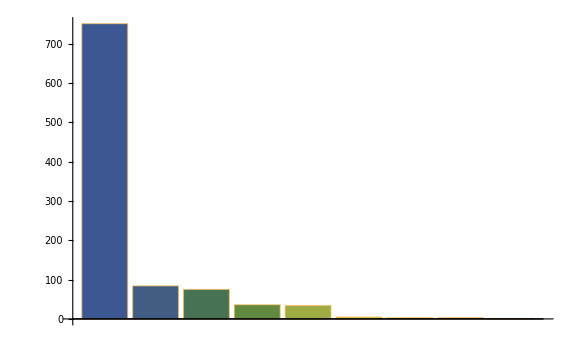

```mathematica
luigidimaio=PlottingCandidate["luigi", "di maio",city->"pomigliano d'arco"]
```

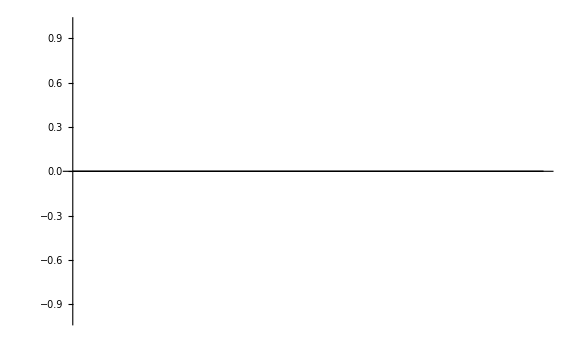

```mathematica
notfound = PlottingCandidate["tommaso","azzalin"]
```

```mathematica
PlottingRegionsItalyMap[]
```

Exporting the image...

...Exported the image!